# A. Stromgren radius, decaying number density

## 0 - Constants

```mathematica
k =8.6173303*^-5; (*ev*);
kmet = 1.38064852*^-23;
kcm  =1.38064852*^-16;
solarLum = 2.38924969*^45;
solarMass  =2*^30;
(*conversion factor from parsec to cm*)
con = 3.08567758*^18; 
mP= 1.6726219*^-27;
planck = 6.62607004*^-34;
alpha[T_] := 2.56*^-13/(T/1*^4)^0.83;
c = 299792458;
```

## 1 - Stromgren for galaxy (constant n)

### 1.1 Basic

```mathematica
StandardForm[HoldForm[(3Q/(4*Pi*a*n^2))]^(1/3)+rSourceCm]
```

rSourceCm+((3 Q)/(4 π a n^2))^(1/3)

```mathematica
rStrom[luminosity_, temp_, rSource_, n_]:= Module[ {Q, rSourceCm}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con;
((3Q/(4*Pi*a*n^2))^(1/3)+rSourceCm)/con]
```

```mathematica
rStrom[2*^10, 1000000, 100000, 0.01] (*answer in pc *)
```

137624.

### 1.2 Temperature by galaxy mass

```mathematica
rStromM[luminosity_, M_, rSource_, n_]:= Module[ {Q, rSourceCm, aMod, T}, rSourceCm:= rSource*con;
T:= 0.59*mP*6.67408*^-11*M*solarMass/(2*1.38064852*^-23*rSourceCm/100);
Q:= luminosity*solarLum/(2.82*T*k); 
aMod:= 2.56*^-13/(T/10^4)^0.83;
{((3Q/(4*Pi*aMod*n^2))^(1/3)+rSourceCm)/con}]
```

```mathematica
rStromM[1.5*^10, 1*^12, 50000, 0.001]
```

{611052.}

## 2 - Exponential and Gaussian decay profiles

2.1 - Decay profiles, n goes to zero, takes temperature as input

### 2.1.1 Constant a

```mathematica
rExp[luminosity_, temp__, rSource_, beta_, n0_]:= Module[ {Q, rSourceCm, a}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con;
a:= 2.56*^-13;
{(Q(3-2*beta)/(4*Pi*a*n0^2)+rSourceCm^(3-2beta))^(1/(3-2beta))}](*answer in pc*)
```

```mathematica
rGauss[luminosity_,temp_,rSource_,d_,n0_]:= Module[{Q, rSourceCm, dCm, a}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con; dCm :=d*con;a:= 2.56*^-13;
 {Solve[Q/(a*4*Pi*n0^2)==Integrate[r^2*Exp[-2r^2/d^2],{r,rSourceCm,rStrom}],rStrom]}]
```

```mathematica
rExp[1.5*^10, 1000000, 5*^4,1.2, 0.001]
```

{6.23593×10^98}

```mathematica
rGauss[2*^10,1000,1*^5,1.5*^24,0.01]
```

{{{rStrom→-1.10322×10^24}}}

### 2.1.2 Temperature dependent a

```mathematica
rExpa[luminosity_, temp_, rSource_, beta_, n0_]:= Module[ {Q, rSourceCm, aMod}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con;
aMod:= 2.56*^-13/(temp/10^4)^0.83;
{(Q(3-2*beta)/(4*Pi*aMod*n0^2)+rSourceCm^(3-2beta))^(1/(3-2beta))/con, Q}]
```

```mathematica
rExpa[2*^10, 10000, 1*^5, 0.7, 0.001]
```

{1.34776×10^27,1.96639×10^55}

2.2 - Non-zero n profiles (constant added so n does not go to zero)

### Exponential

```mathematica
StandardForm[Q/(4*Pi*aMod)==n0^2/(3-2beta)(r^(3-2beta)-rSourceCm^(3-2beta))+2n0*nc*(r^(2-beta)-rSourceCm^(2-beta))+nc^2]
```

Q/(4 aMod π)==nc^2+(n0^2 (r^(3-2 beta)-rSourceCm^(3-2 beta)))/(3-2 beta)+2 n0 nc (r^(2-beta)-rSourceCm^(2-beta))

```mathematica
rExpaC[luminosity_, temp_, rSource_, beta_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con;
aMod:= 2.56*^-13/(temp/10^4)^0.83;
Solve[(Q*(3-2beta)/(4Pi aMod n0^2)+rSource^(3-2beta))^(1/(3-2beta)) == r, r]]
```

```mathematica
rExpaC[2*^10, 10000, 1*^5, 0.1, 0.001, 0.00001]
```

{{r→1.42816×10^26}}

### Gaussian

```mathematica
rGaussaC[luminosity_, temp_, rSource_, d_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con;
aMod:= 2.56*^-13/(temp/10^4)^0.83;
{Solve[Q/(4*Pi*aMod)==Integrate[n0^2r^2Exp[-2r^2/d^2]+2n0*nc*r^2Exp[-r^2/d^2]+nc^2r^2, {r, rSourceCm, rStrom}], rStrom]}]
```

```mathematica
rGaussaC[2*^10,1000,1*^5,1.5*^24,0.01, 0.0001]
```

{{{rStrom→-1.32391×10^26},{rStrom→-1.70792×10^23},{rStrom→1.32562×10^26}}}

2.3 - Non-zero n; temperature mass dependent

#### Exponential

```mathematica
StandardForm[Q/(4*Pi*aMod)==n0^2/(3-2beta)(r^(3-2beta)-rSourceCm^(3-2beta))+2n0*nc/(3-beta)(r^(3-beta)-rSourceCm^(3-beta))+nc^2*(r^3-rSourceCm^3)/3] 
(*equation 19 in the progress report draft*)
```

Q/(4 aMod π)==1/3 nc^2 (r^3-rSourceCm^3)+(n0^2 (r^(3-2 beta)-rSourceCm^(3-2 beta)))/(3-2 beta)+(2 n0 nc (r^(3-beta)-rSourceCm^(3-beta)))/(3-beta)

luminosity is in solar lum, M is in solar masses, rSource in pc, n0 and nc in cm^3. Outputs in cm

```mathematica
rExpaCT[luminosity_, M_, rSource_, beta_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod, T}, rSourceCm:= rSource*con;
T:= 0.59*mP*6.67408*^-11*M*solarMass/(2*1.38064852*^-23*rSourceCm/100); (*equation 23*)
Q:= luminosity*solarLum/(2.82*T*k); 
aMod = 2.56*^-13/(T/1*^4)^0.83;
{(Solve[Q/(4*Pi*aMod)==n0^2/(3-2beta)(r^(3-2beta)-rSourceCm^(3-2beta))+2n0*nc/(3-beta)(r^(3-beta)-rSourceCm^(3-beta))+nc^2*(r^3-rSourceCm^3)/3,r])}]
```

```mathematica
rExpaCT[1.5*^10, 1*^12, 2*^5, 1.2, 0.001, 0.00003]
```

{{{r→-9.69835×10^24-1.6798×10^25 ⅈ},{r→-9.69835×10^24+1.6798×10^25 ⅈ},{r→1.93967×10^25}}}

#### Gaussian

```mathematica
TraditionalForm[Q/(4*Pi*aMod)==HoldForm[Integrate[n0^2r^2Exp[-2r^2/d^2]+2n0*nc*r^2Exp[-r^2/d^2]+nc^2r^2, {r, rSourceCm, rStrom}]]]
(*equation 22 in the progress report draft*)
```

Q/(4 π aMod)==∫_rSourceCm^rStrom (n0^2 r^2 exp(-(2 r^2)/d^2)+2 n0 nc r^2 exp(-r^2/d^2)+nc^2 r^2)ⅆr

```mathematica
rGaussaCT[luminosity_, M_, rSource_, d_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod, T}, rSourceCm:= rSource*con;
T:= 0.59*mP*6.67408*^-11
*M*solarMass/(2*1.38064852*^-23*rSourceCm/100);
Q:= luminosity*solarLum/(2.82*T*k); 
aMod = 2.56*^-13/(T/10^4)^0.83;
{Solve[Q/(4*Pi*aMod)==Integrate[n0^2r^2Exp[-2r^2/d^2]+2n0*nc*r^2Exp[-r^2/d^2]+nc^2r^2, {r, rSourceCm, rStrom}], rStrom]}]
```

```mathematica
rGaussaCT[1.5*^10,1*^12,5*^4,7.71419395*^22,0.001, 0.0001]
```

{{{rStrom→-4.03088×10^24-6.93679×10^24 ⅈ},{rStrom→-4.03088×10^24+6.93679×10^24 ⅈ},{rStrom→8.06175×10^24}}}

2.4 - Stromgren radius as function n and T

### Temperature dependencies

```mathematica
rExpT[luminosity_, T_, rSource_, beta_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod}, rSourceCm:= rSource*con;
(*T:= 0.59*mP*6.67408*^-11*M*solarMass/(2*1.38064852*^-23*rSourceCm/100); (*equation 23*)*)
Q:= luminosity*solarLum/(2.82*T*k); 
aMod :=2.56*^-13/(T/1*^4)^(0.833);
{(Solve[Q/(4*Pi*aMod)==n0^2/(3-2beta)(r^(3-2beta)-rSourceCm^(3-2beta))+2n0*nc/(3-beta)(r^(3-beta)-rSourceCm^(3-beta))+nc^2*(r^3-rSourceCm^3)/3,r])}]
```

```mathematica
rGaussT[luminosity_, T_, rSource_, d_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod}, rSourceCm:= rSource*con;
(*T:= 0.59*mP*6.67408*^-11*M*solarMass/(2*1.38064852*^-23*rSourceCm/100);*)
Q:= luminosity*solarLum/(2.82*T*k); 
aMod = 2.56*^-13/(T/1*^4)^0.83;
{Solve[Q/(4*Pi*aMod)==Integrate[n0^2r^2Exp[-2r^2/d^2]+2n0*nc*r^2Exp[-r^2/d^2]+nc^2r^2, {r, rSourceCm, rStrom}], rStrom]}]
```

```mathematica
(*constant density*)
```

```mathematica
rStromT[luminosity_, T_, rSource_, n_]:= Module[ {Q, rSourceCm, aMod}, rSourceCm:= rSource*con;
Q:= luminosity*solarLum/(2.82*T*k); 
aMod = 2.56*^-13/(T/1*^4)^0.83;
{((3Q/(4*Pi*aMod*n^2))^(1/3)+rSourceCm)/con}]
```

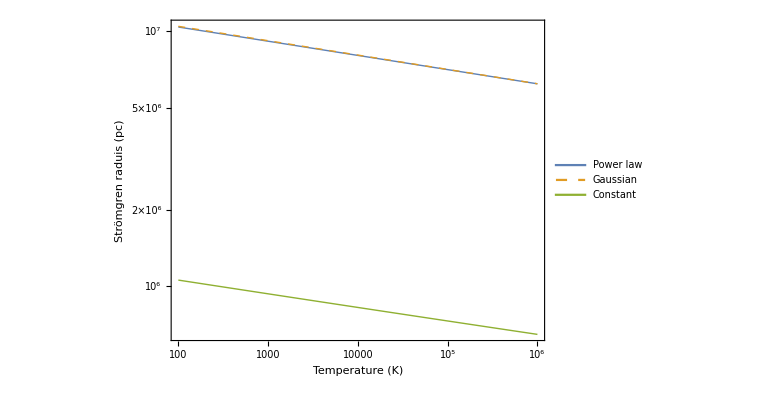

```mathematica
LogLogPlot[{Cases[Flatten[r/.rExpT[1.5*^10, x, 5*^4, 1.2, 0.001, 0.00003]], s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussT[1.5*^10,x,5*^4,7.71419395*^22,0.001, 0.00003]], s_/;Im[s]==0&&s>0]/con , rStromT[1.5*^10, x, 50000, 0.001]}, {x, 100,1000000}, PlotLegends->Placed[
{"Power law", "Gaussian", "Constant"},{0.2,0.5}], AxesLabel->{"Stromgren radius (Pc)", "Temperature (K)"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->{Directive[Thick], Directive[Thick, Dashed],Thick}, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style["Strömgren raduis (pc)",18,FontFamily->"Arial"],None},{Style["Temperature (K)",18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600]
```

### Number density dependencies

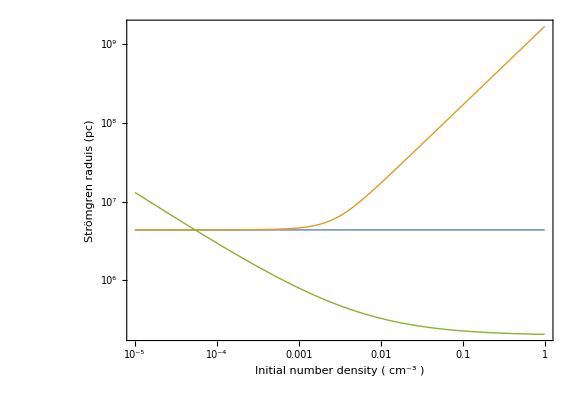

```mathematica
LogLogPlot[{Cases[Flatten[r/.rExpaCT[1.5*^10, 1.5*^12, 2*^5, 1.2, n, 0.00005]], s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1.5*^12,2*^5,3*^23,n, 0.00005]], s_/;Im[s]==0&&s>0]/con, rStromT[1.5*^10, 1000000, 200000, n] }, {n, 0.00001,1},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style["Strömgren raduis (pc)",18,FontFamily->"Arial"],None},{Style[HoldForm["Initial number density ("  Superscript["cm", -3] ")"],18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600]
```

```mathematica
u = LogLogPlot[{Cases[Flatten[r/.rExpaCT[1.5*^10, 1*^12, 5*^4, 1.2, n, 0.00003]], s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1*^12,5*^4,7.71419395*^22,n, 0.00003]], s_/;Im[s]==0&&s>0]/con, rStromM[1.5*^10, 1*^12, 5*^4, n] }, {n, 0.00001,1},  AxesLabel->{ HoldForm["Initial number density"  (cm^3)], "Stromgren radius (Pc)"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->{Thick, Directive[Dashed, Thick], Thick}, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style["Strmögren raduis (pc)",18,FontFamily->"Arial"],None},{Style[HoldForm["Initial number density ("  Superscript["cm", -3] ")"],18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600]
```

# B. Thomson scattering

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

ElectronCharge::shdw: Symbol ElectronCharge appears in multiple contexts {PhysicalConstants`,Global`}; definitions in context PhysicalConstants` may shadow or be shadowed by other definitions.

ElectronMass::shdw: Symbol ElectronMass appears in multiple contexts {PhysicalConstants`,Global`}; definitions in context PhysicalConstants` may shadow or be shadowed by other definitions.

SpeedOfLight::shdw: Symbol SpeedOfLight appears in multiple contexts {PhysicalConstants`,Global`}; definitions in context PhysicalConstants` may shadow or be shadowed by other definitions.

VacuumPermittivity::shdw: Symbol VacuumPermittivity appears in multiple contexts {PhysicalConstants`,Global`}; definitions in context PhysicalConstants` may shadow or be shadowed by other definitions.

### 0 - Constants

```mathematica
(*cross section photon electron in cm^2 *)
sigmaT = 8*^4Pi(ElectronCharge^2/(4Pi VacuumPermittivity*ElectronMass*SpeedOfLight^2))^2/3
```

(6.65246×10^-25 Coulomb^4 Second^2 Volt^2)/(Ampere^2 Kilogram^2 Meter^2)

### 1 - Constant n

```mathematica
rStromM[1.5*^10, 1*^12, 2*^4, 0.001]
```

{552664.}

```mathematica
ThomCon[rStrom_, rSource_, n0_]:= sigmaT*n0*(rStrom-rSource)*con
```

```mathematica
ThomCon[5*^5, 2*^4, 0.001]
```

(0.000985312 Coulomb^4 Second^2 Volt^2)/(Ampere^2 Kilogram^2 Meter^2)

### 2 - Exponential n

```mathematica
ThomExp[rStrom_, rSource_,beta_, n0_, nc_]:= Module[{rSourceCm, rStromCm},rSourceCm = rSource*con; 
rStromCm = rStrom*con; 
sigmaT(n0(rStromCm^(1-beta)-rSourceCm^(1-beta))/(1-beta) +nc(rStromCm-rSourceCm))]
```

```mathematica
ThomExp[1*^6, 5*^4, 1.2, 0.001, 0.00003]
```

(0.0000585029 Coulomb^4 Second^2 Volt^2)/(Ampere^2 Kilogram^2 Meter^2)

### 3 - Gaussian n

```mathematica
ThomGauss[rStrom_, rSource_, d_, n0_, nc_]:=Module[{rSourceCm, rStromCm}, rSourceCm = rSource*con; rStromCm=rStrom*con; 
Solve[tau == sigmaT*Integrate[n0*Exp[-r^2/d^2]+nc, {r,rSourceCm, rStromCm}], tau]]
```

```mathematica
ThomGauss[1*^6, 5*^4, 7.71419395*^22, 0.001, 0.00003]
```

{{tau→(0.0000587157 Coulomb^4 Second^2 Volt^2)/(Ampere^2 Kilogram^2 Meter^2)}}

# C - Mass inside Stromgren sphere

```mathematica
1.38064852*^-23*1*^6*rMW*3.086*^16*1.2/(1000*0.59*mP*6.67408*^-11)
```

{9.71891×10^36}

# D - Stromgren radii local group

## 1. Largest three galaxies

```mathematica
rMW = Cases[Flatten[r/.rExpaCT[1.5*^10, 1*^12, 5*^4, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{1251.98}

```mathematica
rM31= Cases[Flatten[r/.rExpaCT[2.6*^10, 1*^12, 1*^5, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{1564.27}

```mathematica
rM33 = Cases[Flatten[r/.rExpaCT[7.5*^8, 5*^10, 1*^4, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{498.92}

```mathematica
colorz={{Red,Opacity[0.3]},{Blue,Opacity[0.3]},{Green,Opacity[0.3]}};
```

```mathematica
spheres = Graphics3D[{Opacity[0.3], Red, Sphere[{0,0,0}, rMW],Black, Sphere[{0,0,0}, 50],  Blue, Sphere[{-800, 0, 0}, rM31], Black, Sphere[{-800, 0, 0}, 100], Green, Sphere[{-840, 0, -230}, rM33], Black, Sphere[{-840, 0, -230}, 10]}, Axes->True , AxesLabel->{"kpc", "", ""},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16],ImageSize->600];
Legended[Show[spheres],SwatchLegend[{colorz[[1]],colorz[[2]],Green},Style[#,18,FontFamily->"Arial"]&/@{"Milky Way","Andromeda","Triangulum"}]]
```

-Graphics3D-

## 2 - Selected 8 MW satellites

```mathematica
rM82 =  Cases[Flatten[r/.rExpaCT[7.5*^10, 1*^12, 13*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{1983.48}

```mathematica
rLMC= Cases[Flatten[r/.rExpaCT[1*^9, 1*^9, 2*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{625.666}

```mathematica
rSagit= Cases[Flatten[r/.rExpaCT[2*^7, 1*^7, 1.1*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{213.128}

```mathematica
rSMC= Cases[Flatten[r/.rExpaCT[4*^9, 1*^7, 1*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{1239.66}

```mathematica
rBootes= Cases[Flatten[r/.rExpaCT[2*^4, 1*^7, 0.5*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{20.3816}

```mathematica
rSculptor= Cases[Flatten[r/.rExpaCT[2*^6, 1*^7, 0.4*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{93.4137}

```mathematica
rDraco= Cases[Flatten[r/.rExpaCT[3*^5, 1*^7, 0.35*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{49.2593}

```mathematica
colorz={{Red,Opacity[0.3]},{Blue,Opacity[0.3]},{Green,Opacity[0.3]},{Purple,Opacity[0.3]},{Orange,Opacity[0.3]},{Pink,Opacity[0.3]},{Gray,Opacity[0.3]}};
```

```mathematica
spheres = Graphics3D[{Opacity[0.3], Red, Sphere[{0,0,0}, rMW],Black, Sphere[{0,0,0}, 50],  Blue, Sphere[{-10, 20, 5}, rLMC], Black, Sphere[{-10, 20, 5}, 4], Green, Sphere[{2, 0, -5}, rSagit], Black, Sphere[{2, 0, -5}, 1.3], Purple, Sphere[{-8, 30, 5}, rSMC], Black, Sphere[{-8, 30, 5}, 1],Orange, Sphere[{0, -5, 40}, rBootes], Black, Sphere[{0, -5, 40}, 0.5], Pink, Sphere[{-3, 50, -10}, rSculptor], Black, Sphere[{-3, 50, -10}, 0.4], Gray, Sphere[{10, 0, 40}, rDraco], Black, Sphere[{10, 0, 40}, 0.35]}, Axes->True , AxesLabel->{"kpc", "", ""},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16]];
Legended[Show[spheres],SwatchLegend[{colorz[[1]],colorz[[2]],Green},Style[#,18,FontFamily->"Arial"]&/@{"Milky Way","Andromeda","Triangulum"}]]
```

-Graphics3D-

2.1 - Large satellites

```mathematica
spheres = Graphics3D[{Opacity[0.3], Red, Sphere[{0,0,0}, rMW],Black, Sphere[{0,0,0}, 50],  Blue, Sphere[{-10, 20, 5}, rLMC], Black, Sphere[{-10, 20, 5}, 4], Green, Sphere[{2, 0, -5}, rSagit], Black, Sphere[{2, 0, -5}, 1.3], Yellow, Sphere[{-8, 30, 5}, rSMC], Black, Sphere[{-8, 30, 5}, 1]}, Axes->True , AxesLabel->{"kpc", "", ""}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16], ImageSize->600];
Legended[Show[spheres],SwatchLegend[{colorz[[1]],colorz[[2]],Green, Yellow},Style[#,18,FontFamily->"Arial"]&/@{"Milky Way","Large Magellanic Cloud","Sagittarius","Small Magellanic Cloud"}]]
```

-Graphics3D-

2.2 - Smaller satellites

```mathematica
spheres = Graphics3D[{Opacity[0.3],Black, Sphere[{0,0,0}, 50],  Orange, Sphere[{0, -5, 40}, rBootes], Black, Sphere[{0, -5, 40}, 0.5], Pink, Sphere[{-3, 50, -10}, rSculptor], Black, Sphere[{-3, 50, -10}, 0.4], Green, Sphere[{10, 0, 40}, rDraco], Black, Sphere[{10, 0, 40}, 0.35]}, Axes->True , AxesLabel->{"kpc", "", ""}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16], ImageSize->600];
Legended[Show[spheres],SwatchLegend[{Orange,Pink,Green},Style[#,18,FontFamily->"Arial"]&/@{"Bootes III","Sculptor","Draco"}]]
```

-Graphics3D-

# F - Intensity

## 1. Intensity over one line

```mathematica
lineIntensity[n0_,nc_, d_] := 5.4*^-39*Integrate[(n0(d*Sec[theta])^-2.4+nc)^2d Sec[theta]^2, {theta, 0, ArcCos[d/(800*^3*con)]}]/Sqrt[1*^7]
```

```mathematica
Plot[{x*lineIntensity[0.001,0.00003,100*^3*con]*Exp[-planck*x/(kmet*1*^7)],x*lineIntensity[0.001,0.00003,400*^3*con]*Exp[-planck*x/(kmet*1*^7)],x*lineIntensity[0.001,0.00003,600*^3*con]*Exp[-planck*x/(kmet*1*^7)]}, {x,1*^6,1*^18}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["ν" Subscript["I","ν"] "(erg"Superscript["cm", -2]Superscript["s", -1]Superscript["str", -1]")"],18,FontFamily->"Arial"],None},{Style[HoldForm["ν (Hz)"],18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600, PlotLegends->LineLegend[Automatic,{"100 kpc", "400 kpc", "600 kpc"}]]
```

-Graphics-

## 2. Intensity summed over lines

```mathematica
intensity[n0_,nc_, d_, rStrom_] := 5.4*^-39*Integrate[(n0(d*Sec[theta])^-2.4+nc)^2d Sec[theta]^2, {theta, 0, ArcCos[d/(rStrom*10^3*con)]}]/Sqrt[1*^7]
```

```mathematica
corrFac[pixelWidth_, pixelHeight_, radius_]:= Module[{width, height, correction, gridElements,d, dCm, intensities}, 
width:= radius*2/(Sqrt[2]*(pixelWidth -1)); 
height:= width;
correction:= 4*Pi*width*height;
gridElements:= Tuples[{Range[1,pixelWidth/2-1],Range[1,pixelHeight/2-1]}];
d :=Apply[{Sqrt[(#1*width)^2+(#2*height)^2]}&,gridElements,{1}];
dCm:= d*10^3*con; 
intensities:=correction*intensity[0.001,0.00003, #[[1]], radius]&/@dCm; 
4*Total[intensities]]
```

```mathematica
int400= corrFac[16,16, 400];
int800= corrFac[16,16, 800];
int1000= corrFac[16,16, 1000];
```

```mathematica
Plot[{x*int400*Exp[-planck*x/(kmet*1*^7)],x*int800*Exp[-planck*x/(kmet*1*^7)],x*int1000*Exp[-planck*x/(kmet*1*^7)]}, {x,1*^6,1*^18}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["ν" Subscript["I","ν"] "(erg"Superscript["cm", -2]Superscript["s", -1]")"],18,FontFamily->"Arial"],None},{Style[HoldForm["ν (Hz)"],18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600, PlotLegends->LineLegend[Automatic,{"400 kpc", "800 kpc", "1000 kpc"}]]
```

-Graphics-

## 3. Flux

```mathematica
flux[n0_,nc_,  D_, rStrom_, phi_] := 2*Pi*5.4*^-39*NIntegrate[(n0(D*Tan[phi]*Sec[theta])^-2.4+nc)^2D*Tan[phi]* Sec[theta]^2*Sin[phi]^2, {theta, 0, ArcCos[D*Tan[phi]/rStrom]}]/Sqrt[1*^7]
```

```mathematica
Table[{x,flux[0.001, 0.0005, 200*^3*con,1000*^3*con, x]},{x,0.0001,ArcTan[1000/ 200],0.1}]
```

{{0.0001,8.27683×10^-32},{0.1001,8.26406×10^-26},{0.2001,3.26736×10^-25},{0.3001,7.21915×10^-25},{0.4001,1.25125×10^-24},{0.5001,1.89172×10^-24},{0.6001,2.61476×10^-24},{0.7001,3.38672×10^-24},{0.8001,4.16874×10^-24},{0.9001,4.91544×10^-24},{1.0001,5.56964×10^-24},{1.1001,6.04541×10^-24},{1.2001,6.16553×10^-24},{1.3001,5.32761×10^-24}}

```mathematica
interpolatedFlux  = Interpolation[%]
```

InterpolatingFunction[{{0.0001, 1.3001}}, <>]

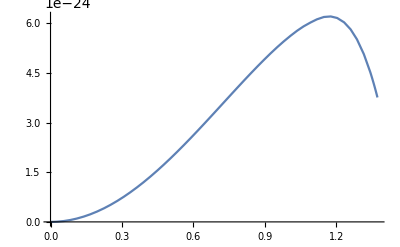

```mathematica
Plot[interpolatedFlux[x],{x,0.0001,ArcTan[1000/ 200]}]
```

```mathematica
totalFlux = Integrate[interpolatedFlux[x], {x,0.0001,ArcTan[1000/ 200]}]
```

InterpolatingFunction::dmvali: The integration endpoint ArcTan[5] in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

4.33266×10^-24

```mathematica
Plot[totalFlux*Exp[-planck*x/(kmet*1*^7)] ,{x,1*^6,1*^16}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["ν" Subscript["I","ν"] "(erg"Superscript["cm", -2]Superscript["s", -1]Superscript["str", -1]")"],18,FontFamily->"Arial"],None},{Style[HoldForm["ν (Hz)"],18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600, PlotLegends->LineLegend[Automatic,{"100 kpc", "800 kpc", "1000 kpc"}]]
```

-Graphics-

```mathematica
fluxByDist[D_]:= Module[{table, interpolatedFlux}, 
table:= Table[{x,flux[0.001, 0.0005, D,1000*^3*con, x]},{x,0.0001,ArcTan[1000/ 200],0.1}]; 
interpolatedFlux= Interpolation[table];
Integrate[interpolatedFlux[x], {x,0.0001,ArcTan[1000/ 200]}]]
```

InterpolatingFunction::dmvali: The integration endpoint ArcTan[5] in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

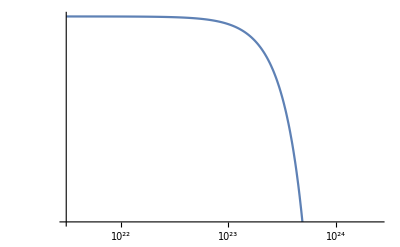

```mathematica
LogLogPlot[fluxByDist[d], {d, 1*^3*con, 800*^3*con}]
```

# G. Heating and cooling

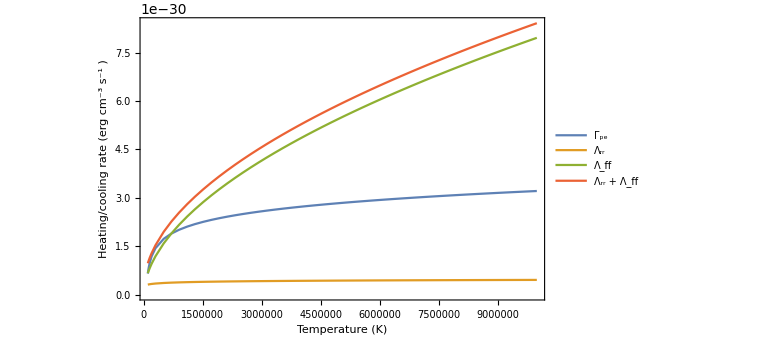

```mathematica
Plot[{(2.8214 - 2.18*^-11/(kcm*T))*alpha[T]*0.001^2*kcm*T,alpha[T]*0.001^2*(0.684-0.0416Log[T/1*^4])*kcm*T, alpha[T]*0.001^2*0.54*(T/1*^4)^0.37*kcm*T, alpha[T]*0.001^2*(0.684-0.0416Log[T/1*^4])*kcm*T+ alpha[T]*0.001^2*0.54*(T/1*^4)^0.37*kcm*T}, {T, 1*^5, 1*^7}, PlotLegends->LineLegend[Automatic,{Style[HoldForm[Subscript["Γ","pe"]]],Style[HoldForm[Subscript["Λ","rr"]]], Style[HoldForm[Subscript["Λ","ff"]]], Style[HoldForm[Subscript["Λ","rr"]"+"Subscript["Λ","ff"]]]}], LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["Heating/cooling rate (erg"Superscript["cm", -3]Superscript["s", -1]")"],18,FontFamily->"Arial"],None},{Style[HoldForm["Temperature (K)"],18,FontFamily->"Arial"],None}}]
```

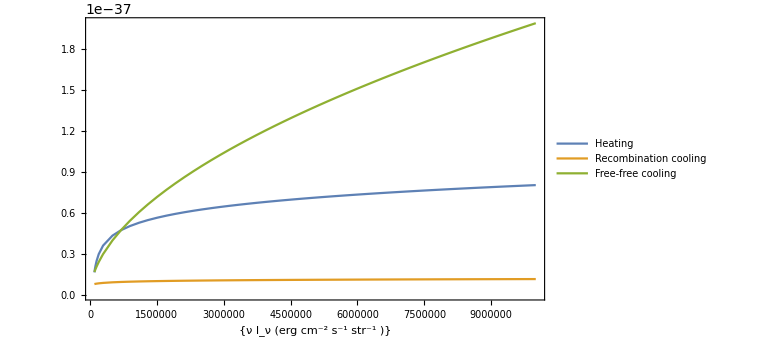

```mathematica
Plot[{(2.8214 - 2.18*^-18/(kmet*T))*alpha[T]*0.0005^2*kmet*T,alpha[T]*0.0005^2*(0.684-0.0416Log[T/1*^4])*kmet*T, alpha[T]*0.0005^2*0.54*(T/1*^4)^0.37*kmet*T}, {T, 1*^5, 1*^7}, PlotLegends->LineLegend[Automatic,{"Heating", "Recombination cooling", "Free-free cooling"}], LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["ν" Subscript["I","ν"] "(erg"Superscript["cm", -2]Superscript["s", -1]Superscript["str", -1]")"],18,FontFamily->"Arial"]}}]
```

# H. Front evolution

## 1. Velocity

```mathematica
velocity[luminosity_,M_, rSource_, beta_,n0_,nc_,T0_,r_]:=Module[ {Q, rSourceCm, aMod, T, rCm, speed, soundspeed}, rSourceCm:= rSource*con;
rCm := r*con*1*^3+rSourceCm;
T:= 0.59*mP*6.67408*^-11*M*solarMass/(2*1.38064852*^-23*rSourceCm/100); (*equation 23*)
Q:= luminosity*solarLum/(2.82*T*k); 
aMod :=2.56*^-13/(T/1*^4)^(0.833);
speed:=(Q/(4Pi(rCm-rSourceCm)^2(n0*rCm^-beta+nc)) - aMod*(n0*rCm^-beta+nc)(rCm-rSourceCm)/3 )/1*^3;
If[speed>3*^8, speed = 299792458, speed=speed];
soundspeed:= Sqrt[kmet/mP]*(Sqrt[2*T]+Sqrt[2*T-T0]);
If[speed<soundspeed, speed = soundspeed, speed=speed];
speed]
```

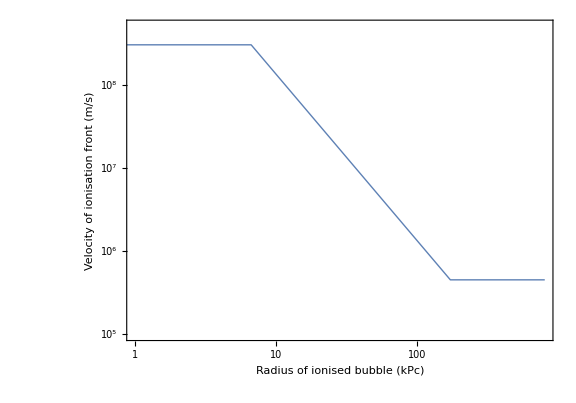

```mathematica
LogLogPlot[velocity[1.5*^10, 1*^12, 5*^4, 1.2, 0.001, 0.00003, 1*^4,r], {r, 0.1, 800}, PlotRange->{{1,800},{1*^5,5*^8}},    LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->{Directive[Thick]}, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style["Velocity of ionisation front (m/s)",18,FontFamily->"Arial"],None},{Style["Radius of ionised bubble (kPc)",18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600]
```

## 2. Radius vs. time

```mathematica
timeSteps = Table[0.01*10*con/velocity[1.5*^10, 1*^12, 5*^4, 1.2, 0.001, 0.00003,1*^4, x], {x,0.1, 800, 0.01}];
```

```mathematica
timeVals = Accumulate[timeSteps]/(3600*24*365);
```

```mathematica
data = Transpose[{Table[x, {x,0.1, 800, 0.01}], timeVals}];
```

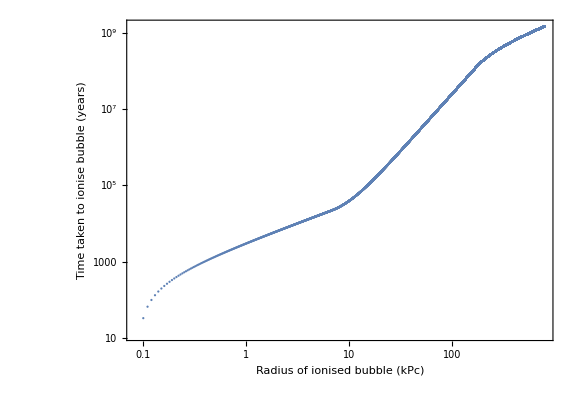

```mathematica
ListLogLogPlot[data,    LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->{Directive[Thick]}, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["Time taken to ionise bubble"" " "(years)"],18,FontFamily->"Arial"],None},{Style["Radius of ionised bubble (kPc)",18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600]
```

## 3. Sound speed

```mathematica
soundSpeedInside[T_]:= Sqrt[(5/3)*2*kmet*T/mP]
```

```mathematica
soundSpeedInside[1*^6]
```

165875.

```mathematica
soundSpeedOutside[T_]:= Sqrt[(5/3)*kmet*T/mP]
```

```mathematica
soundSpeedOutside[1*^4]
```

11729.2

## 4. Stagnation radius and mass

```mathematica
rStag = 1000(8/3)^(2/3)(soundSpeedInside[1*^6]/soundSpeedOutside[1*^4])^(4/3)
```

65765.7

```mathematica
mStag = 4Pi*1000^3*^3*3*^16(8/3)^(8/3)(soundSpeedInside[1*^6]/soundSpeedOutside[1*^4])^(8/3)/3
```

2.00986310360908×10^9021

# I. Psi value

These integrals converge faster when the constants are not defined

```mathematica
bUp[v_,t_]:= 2*v^2(h*v-h*v0)/(cs^2)(Exp[h*v/(kb*t)]-1)^-1;
```

```mathematica
Integrate[bUp[v,t], {v,0,Infinity}, Assumptions->Re[h/(kb*t)>0]]
```

ConditionalExpression[(2 kb^3 t^3 (kb π^4 t-30 h v0 Zeta[3]))/(15 cs^2 h^3),Re[h/(kb t)]>0]

```mathematica
bDown[v_,t_]:= 2*v^2/(cs^2)(Exp[h*v/(kb*t)]-1)^-1;
```

```mathematica
Integrate[bDown[v,t], {v,0,Infinity}, Assumptions->Re[h/(kb*t)>0]]
```

ConditionalExpression[(4 kb^3 t^3 Zeta[3])/(cs^2 h^3),Re[h/(kb t)]>0]